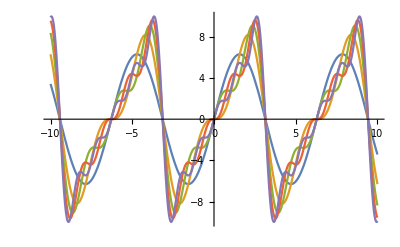

```mathematica
f[x_]:=x;

a[n_]:=Integrate[f[x] Cos[n x],{x,-Pi , Pi}];
b[n_]:=Integrate[f[x] Sin[n x],{x,-Pi , Pi}];

four[x_,k_]:= a[0]/2 + Sum[ a[n] Cos[n x] + b[n] Sin[n x],{n,1,k}];

Plot[Evaluate[Table[ four[x,k],{k,1,5}]],{x,-10,10}]
```

```mathematica
(* -----------------------------*)
```

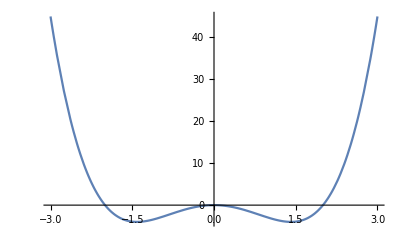

{0,-mu^2/(4 lambda),-mu^2/(4 lambda)}

-Graphics3D-

```mathematica
V[mu_,lambda_,x_]:= -mu x^2 + lambda x^4;
Plot[ V[4,1,x],{x,-3,3}]

Vst[x_]=D[V[mu,lambda,x],x];
mM= Solve[Vst[x]==0,x];
valmM= V[mu,lambda,x]/.mM

ParametricPlot3D[ w=V[4,1,r];
                       {r Sin[phi], r Cos[phi] , w}, {r,0,2},{phi,0,2 Pi}]
```

```mathematica
(* ----------------------------- *)
```

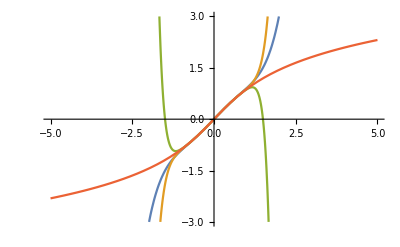

```mathematica
sv[n_]:= Normal[Series[ArcSinh[x],{x,0,n}]];

funss = Join[Table[sv[i],{i,{5,9,11}}],{ArcSinh[x]}];

Plot[funss , {x,-5,5} , PlotRange->{-3,3}]
```